## State

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
(*MatrixForm[H=ImportArmaBinary["H.bin"]];
MatrixForm[Px=ImportArmaBinary["Px.bin"]];
MatrixForm[Py=ImportArmaBinary["Py.bin"]];*)
MatrixForm[w=ImportArmaBinary["w.bin"][[1]]];
(*MatrixForm[w0=ImportArmaBinary["w0.bin"][[1]]];*)
MatrixForm[psi=ImportArmaBinary["psi.bin"]];
(*Norm[H.Px-Px.H]
Norm[H.Py-Py.H]
Tally[w0,Norm[#1-#2]<1.*^-7&];
Select[%,#[[2]]>1&]*)
```

```mathematica
plotWF[psi0_]:=Module[{psi, max,L,x,y},
max=Max[Abs[psi0]];
L=Sqrt[Length[psi0]/2];
psi=ArrayReshape[psi0,{L,L,2}];
psi=(psi/max+1)/2;
Graphics[{
AbsoluteThickness[4],
Table[
{Blend[{Red,White,Blue},psi[[y+1,x+1,1]]],
Line[{{x,y},{x+1,y}}],
Blend[{Red,White,Blue},psi[[y+1,x+1,2]]],
Line[{{x,y},{x,y+1}}]}
,{x,0,L-1},{y,0,L-1}]
},Background->GrayLevel[0.8]]
]
```

```mathematica
TableForm[Transpose[{Range[1,Length[w0]],w0}]]
```

```mathematica
i=127;
{w0[[i]],w0[[i+1]]}
plotWF[psi[[i]]]
plotWF[psi[[i+1]]]
Clear[i]
```

## Rotate face

```mathematica
plotParticles[p0_]:=Module[{p,q, L,x,y,Nf},
L=Sqrt[Length[p0]/2];
p=ArrayReshape[p0,{L,L,2}];
Nf=(Max[p]-1)/2;
Graphics[{
Table[
{
q=p[[y+1,x+1,1]];
Switch[q
,0,{Black,AbsoluteThickness[1],Line[{{x,y},{x+1,y}}]}
,1,{Black,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}]}
,pp_/;pp≤Nf+1,{Red,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}],Text[q-2,{x+0.5,y},{0,-1.5}]}
,pp_/;pp≤2Nf+1,{Blue,AbsoluteThickness[5],Line[{{x,y},{x+1,y}}],Text[q-2-Nf,{x+0.5,y},{0,-1.5}]}
],
q=p[[y+1,x+1,2]];
Switch[q
,0,{Black,AbsoluteThickness[1],Line[{{x,y},{x,y+1}}]}
,1,{Black,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}]}
,pp_/;pp≤Nf+1,{Red,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}],Text[q-2,{x,y+0.5},{-1.5,0}]}
,pp_/;pp≤2Nf+1,{Blue,AbsoluteThickness[5],Line[{{x,y},{x,y+1}}],Text[q-2-Nf,{x,y+0.5},{-1.5,0}]}
]
}
,{x,0,L-1},{y,0,L-1}],
Black,
Table[
Text[x+L*y,{x+0.5,y+0.5}]
,{x,0,L-1},{y,0,L-1}]
},
BaseStyle->{FontSize->12},
ImageSize->300
]
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
Run["./run"];
p=ImportArmaBinary["p.bin"];
GraphicsRow[plotParticles/@p]
```

## Correct distribution

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
p=ImportArmaBinary["p.bin"];
ListPlot[p,PlotStyle->AbsolutePointSize[1]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
(*Run["./run"];*)
tally=ImportArmaBinary["tally.bin"];
ListPlot[Sort[tally],PlotRange->All]
```

```mathematica
Select[tally,Norm[#[[1]]-tally[[4,1]]]<1.*^-7&]
```

```mathematica
w=Flatten[Table[i,{i,1,6},{RandomInteger[{100,200}]}]];
w=Table[Random[],{200}];
b=Accumulate[w];
b=N[b/Max[b]];
ls=Table[
x=Random[];
i=1;
While[i<=Length[b]&&b[[i]]<x,i++];
i
,{5000}];
tally=Tally[ls];
ListPlot[Transpose[{w[[tally[[All,1]]]],tally[[All,2]]}]]
Clear[w,b,ls,i,x]
```

## Swap states

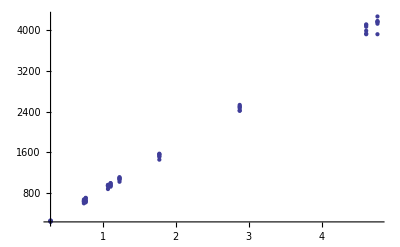

```mathematica
SetDirectory[NotebookDirectory[]];
<<ArmaBinary`
(*Run["./run"];*)
tally=ImportArmaBinary["tally.bin"];
ListPlot[Sort[tally],PlotRange->All]
```